```mathematica
latSecs := 60 * 60 * 180
longSecs := 60 * 60 * 360
```

```mathematica
speedMin := 1
speedMax := 1
```

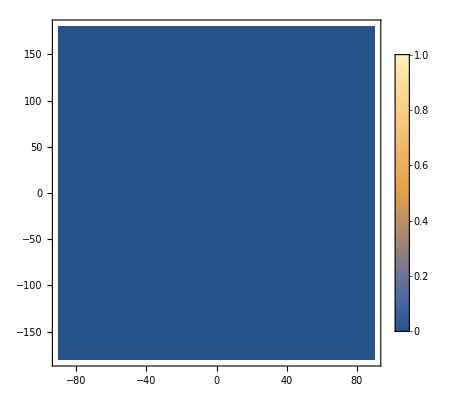

```mathematica
DensityPlot[{1/latSecs/longSecs}, {lat, -90, 90}, {long, -180, 180},PlotLegends->Automatic]
```

```mathematica
latTarget := 0
longTarget := 0
maxEta := 25
eta[aLat_, aLong_, bLat_, bLong_, speed_] := ((aLat - bLat)^2 + (aLong-bLong)^2)^(1/2) / speed
pointsInRange = Sum[If[eta[lat, long, latTarget, longTarget, 1] ≤ maxEta, 1, 0],{lat, -90, 90}, {long, -180, 180}] 
pointsNotInRange = latSecs * longSecs - pointsInRange
```

1961

839807998039

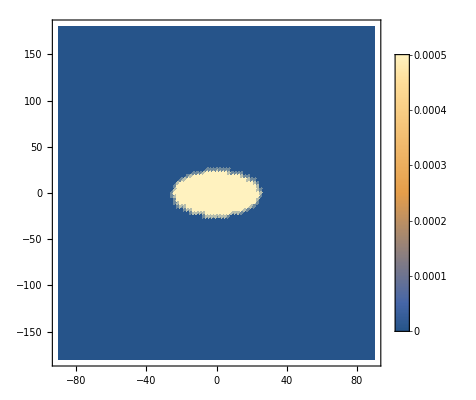

```mathematica
DensityPlot[{If[eta[latTarget,longTarget, lat, long, 1] ≤ maxEta, 1/pointsInRange, 0]}, {lat, -90, 90}, {long, -180, 180},PlotPoints->100,PlotLegends->Automatic]
```

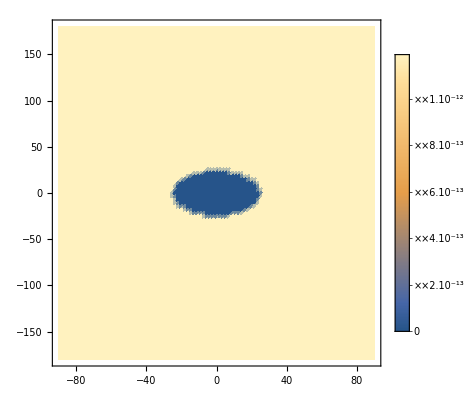

```mathematica
DensityPlot[{If[eta[latTarget,longTarget, lat, long, 1] > maxEta, 1/pointsNotInRange, 0]}, {lat, -90, 90}, {long, -180, 180},PlotPoints->100,PlotLegends->Automatic]
```